```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->16, Black},ImageSize->Large,PlotStyle->Thick];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16,Black},LabelStyle->Black,ImageSize->Large,PlotStyle->Thick];
```

Derive Klein-Nashina “true” Compton distribution over scattering angle θ = [π/2,π] as we only care about the actual edge near the maximum transferred energy

```mathematica
r0 = Entity["Particle","Electron"][EntityProperty["Particle","ClassicalRadius"]];
```

```mathematica
m0 = Entity["Particle","Electron"][EntityProperty["Particle","Mass"]];
```

```mathematica
c = Quantity[, "SpeedOfLight"];
```

Input energy of gamma rays, currently set to 0.6617 MeV for Cesium 137 source

```mathematica
En = Quantity[0.6617, "Megaelectronvolts"];
```

Energy of scattered electron with respect to input gamma energy and scattering angle θ in MeV, this is the energy that goes into the scintillator

```mathematica
Ene[θ_]:= En-((En*m0*c^2)/(m0*c^2+En*(1-Cos[θ])))
```

Energy of the scattered gamma ray

```mathematica
Enp[θ_]:=En-Ene[θ]
```

One of many g[θ]  (imperially defined functions)

```mathematica
g[θ_] := 1/2(Enp[θ]/En)^2(Enp[θ]/En+En/Enp[θ]-Sin[θ]^2)
```

Compton scattering cross section in cm^2/MeV

```mathematica
dsEne[θ_]:=(2π r0^2 Sin[θ] g[θ])(((1+En/(m0*c^2)*(1-Cos[θ]))^2*m0*c^2)/(En^2*Sin[θ]))
```

Calculate some points from the “true” distribution for polynomial fitting, show max scattered energy and max cross section, both at the end of the plot
This max scattered energy is the theoretical ideal location for the Compton edge

```mathematica
mixedpoints = Table[{Ene[θ],UnitConvert[dsEne[θ],Quantity[, ("Centimeters")^2/("Megaelectronvolts")]]},{θ,π/2,π,0.01}];
```

```mathematica
minscatteredenergy=QuantityMagnitude[Min[mixedpoints[[All,1]]]]
```

0.373367

```mathematica
maxscatteredenergy =QuantityMagnitude[Max[mixedpoints[[All,1]]]]
```

0.477374

```mathematica
maxcrosssection = QuantityMagnitude[Max[mixedpoints[[All,2]]]]
```

1.12627×10^-24

Setup simple 2nd order polynomial piecewise model to represent ideal Compton edge

```mathematica
modelr[en_] = Piecewise[{{a1*en^2+b1*en+c1, en<=enc}, {0, en>enc}}];
```

For ease of fitting, use a normal 2nd order polynomial to get coefficients

```mathematica
twodpoly = a1*x^2+b1*x+c1;
```

```mathematica
fitparams=FindFit[QuantityMagnitude[mixedpoints],twodpoly,{a1,b1,c1},x]
```

{a1→5.78912×10^-23,b1→-4.35974×10^-23,c1→8.73626×10^-24}

Todo: use “Plot Diagnostics for Fitted Models” to get linear fit residuals

Now that the simple piecewise model has correct coefficients, convolve it with a Gaussian to get a more realistic understanding of the detector system including resolution and other uncorrelated Gaussian noise, from photopeaks for example.

```mathematica
gaussian[en_]=PDF[NormalDistribution[0,σ],en]
```

(ⅇ^(-en^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
cmodelr[en_]=Convolve[modelr[en],gaussian[en],en,en2];
```

```mathematica
Simplify[cmodelr[en],a1>0&&b1>0&&c1>0&&σ>0&&en2>0&&enc>0]
```

1/2 (c1+b1 (en2-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)+a1 (en2^2-ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2+enc) √(2/π) σ+σ^2)-(c1+b1 en2+a1 (en2^2+σ^2)) Erf[(en2-enc)/(√2 σ)])

Now plot it all! We have to pick some Gaussian to describe how good the detector resolution and how dominant other noise sources are, for this we’ll use 0.1 .

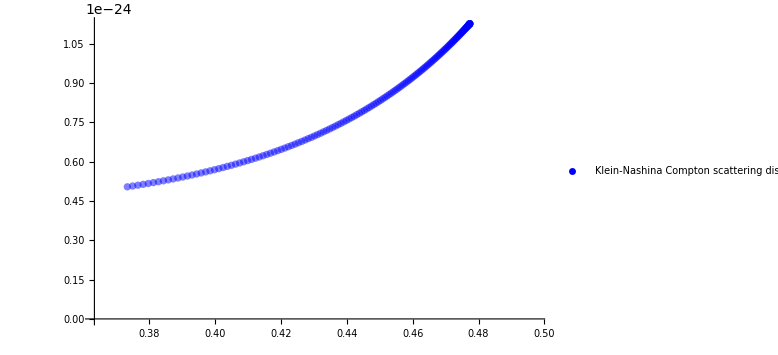

```mathematica
kndistplot =ListPlot[mixedpoints,PlotRange->{{minscatteredenergy-0.01,maxscatteredenergy+0.02},Full},PlotStyle->Opacity[0.5,Blue],PlotLegends->Placed[PointLegend[{Blue},{"Klein-Nashina Compton scattering distribution"}],Bottom]]
```

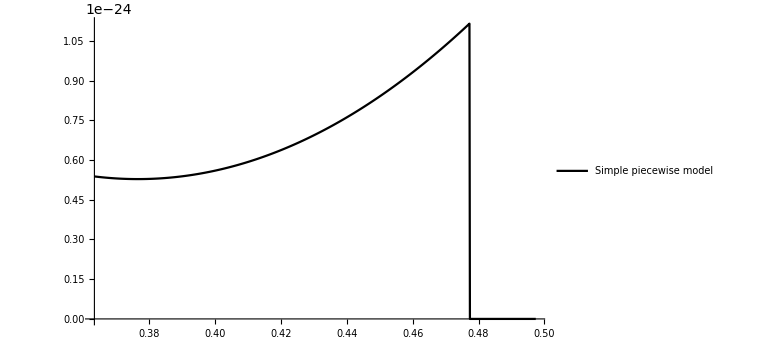

```mathematica
fittedmodelplot =Plot[modelr[en]/.Join[fitparams,{enc->maxscatteredenergy,σ->0.005}],{en,minscatteredenergy-0.01,maxscatteredenergy+0.02},PlotRange->{{minscatteredenergy-0.01,maxscatteredenergy+0.02},Full},PlotStyle->{Black,Thick},PlotPoints->1000,PlotLegends->Placed[LineLegend[{"Simple piecewise model"}],Bottom]]
```

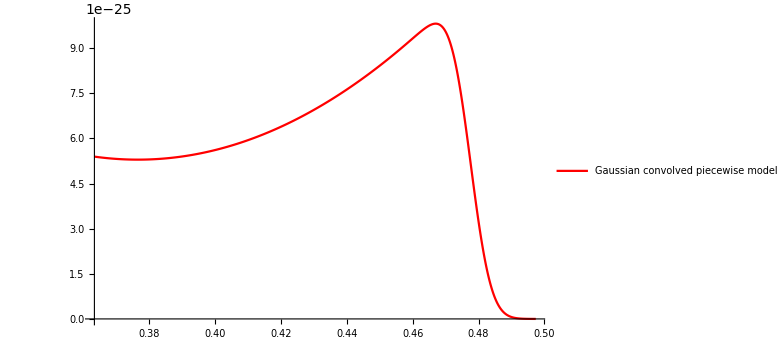

```mathematica
fittedconvolvedmodelplot=Plot[cmodelr[en]/.Join[fitparams,{enc->maxscatteredenergy,σ->0.005}],{en2,minscatteredenergy-0.01,maxscatteredenergy+0.02},PlotRange->{{minscatteredenergy-0.01,maxscatteredenergy+0.02},Full},PlotStyle->Red,PlotPoints->1000,PlotLegends->Placed[LineLegend[{"Gaussian convolved piecewise model"}],Bottom]]
```

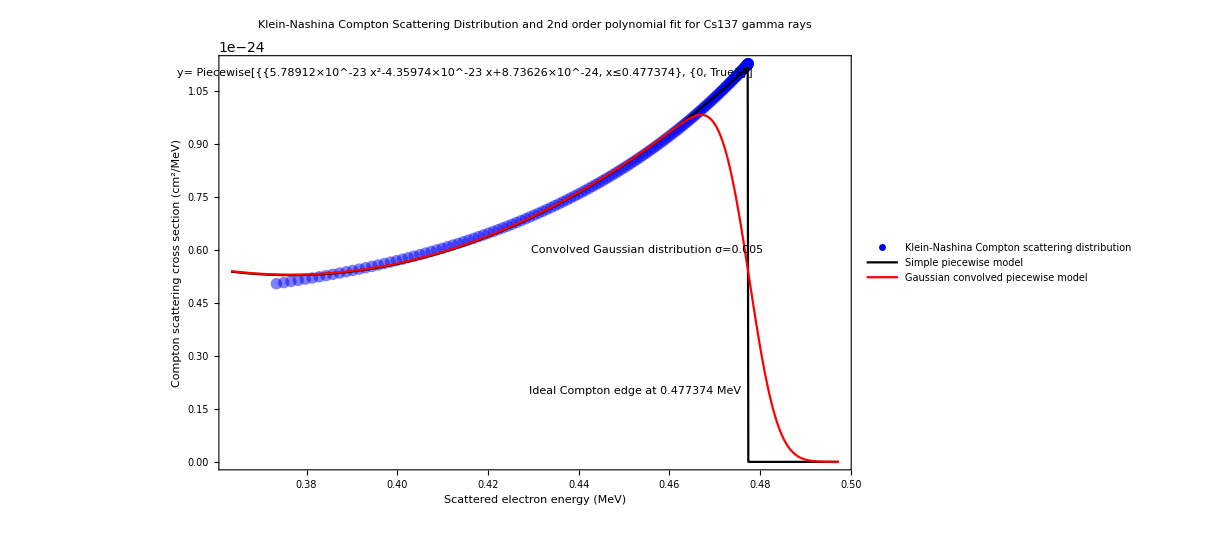

```mathematica
Show[kndistplot,fittedmodelplot,fittedconvolvedmodelplot,GridLines->{{{maxscatteredenergy,Thick}},{}},Frame->{True,True,False,False},FrameLabel->{"Scattered electron energy (MeV)","Compton scattering cross section (cm^2/MeV)"},Axes->False,PlotLabel->Pane["Klein-Nashina Compton Scattering Distribution and 2nd order polynomial fit for Cs137 gamma rays",Alignment->Center],ImageSize->900,
Epilog->{
Text[Style[StringForm["Ideal Compton edge at `` MeV",maxscatteredenergy],Black],{maxscatteredenergy-0.025,2*10^-25}],
Text[Style[StringForm["Simple piecewise polynomial model with fitting:"],Black],{0.415,12*10^-25}],
Text[Style[StringForm["y= ``",modelr[x]/.Join[fitparams,{enc->maxscatteredenergy}]],Black],{0.415,11*10^-25}],
Text[Style[StringForm["Convolved Gaussian distribution σ=``",0.005],Black],{0.455,6*10^-25}]
}]
```

Differentiate the convolved model to demonstrate how close the minimum is to the true Compton edge

```mathematica
scmodelr=Simplify[cmodelr[en],a1>0&&b1>0&&c1>0&&σ>0&&en2>0&&enc>0]
```

1/2 (c1+b1 (en2-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)+a1 (en2^2-ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2+enc) √(2/π) σ+σ^2)-(c1+b1 en2+a1 (en2^2+σ^2)) Erf[(en2-enc)/(√2 σ)])

```mathematica
dscmodelr=D[scmodelr,en2]
```

1/2 (b1 (1+(ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2-enc) √(2/π))/σ)+a1 (2 en2+(ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2-enc) (en2+enc) √(2/π))/σ-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)-(ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) (c1+b1 en2+a1 (en2^2+σ^2)))/σ-(b1+2 a1 en2) Erf[(en2-enc)/(√2 σ)])

Scale fit parameters for y axis in order to get a reasonable result that can be represented on the same plot as the earlier work

```mathematica
fitparams
```

{a1→5.78912×10^-23,b1→-4.35974×10^-23,c1→8.73626×10^-24}

```mathematica
fitparamsscaled ={a1->5.646981085514258*^-23*10^□,b1->-4.303507488054951*^-23,c1->8.721055534912068*^-24}
```

{a1→5.64698×10^-23 10^□,b1→-4.30351×10^-23,c1→8.72106×10^-24}

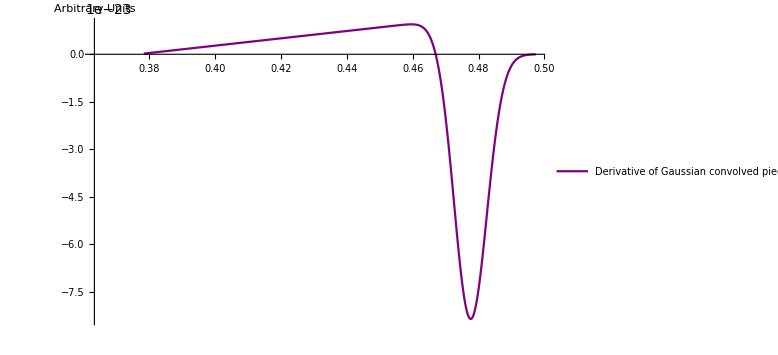

```mathematica
derfittedconvolvedmodelplot=Plot[dscmodelr/.Join[fitparams,{enc->maxscatteredenergy,σ->0.005}],{en2,minscatteredenergy+0.005,maxscatteredenergy+0.02},PlotRange->{{minscatteredenergy-0.01,maxscatteredenergy+0.02},Full},PlotStyle->Purple,PlotPoints->1000, PlotLegends->Placed[LineLegend[{"Derivative of Gaussian convolved piecewise model"}],Bottom],AxesLabel->{"","Arbitrary Units"}]
```

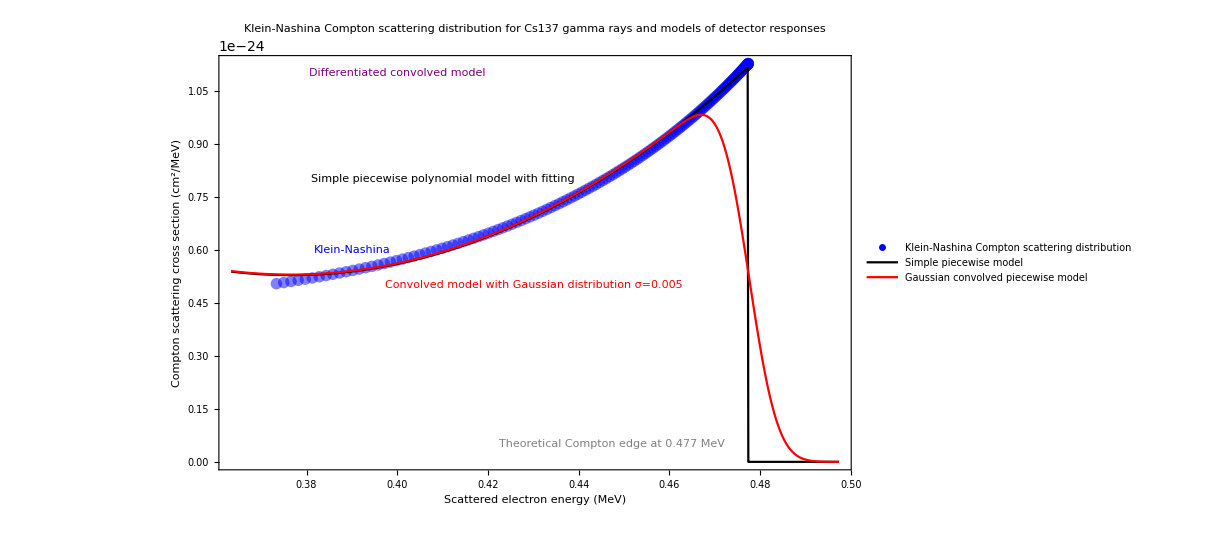

```mathematica
comboplot=Show[kndistplot,fittedmodelplot,fittedconvolvedmodelplot,PlotRange->Full,GridLines->{{{maxscatteredenergy,Thick}},{}},Frame->{True,True,False,False},FrameLabel->{"Scattered electron energy (MeV)","Compton scattering cross section (cm^2/MeV)"},Axes->False,PlotLabel->Pane["Klein-Nashina Compton scattering distribution for Cs137 gamma rays and models of detector responses",Alignment->Center],ImageSize->900,
Epilog->{
Text[Style[StringForm["Theoretical Compton edge at `` MeV","0.477"],Gray],{maxscatteredenergy-0.03,0.5*10^-25}],
Text[Style[StringForm["Simple piecewise polynomial model with fitting"],Black],{0.410,8*10^-25}],
Text[Style[StringForm["Convolved model with Gaussian distribution σ=``",0.005],Red],{0.43,5*10^-25}],Text[Style[StringForm["Klein-Nashina"],Blue],{0.39,6*10^-25}],
Text[Style[StringForm["Differentiated convolved model"],Purple],{0.40,1.1*10^-24}]
}]
```

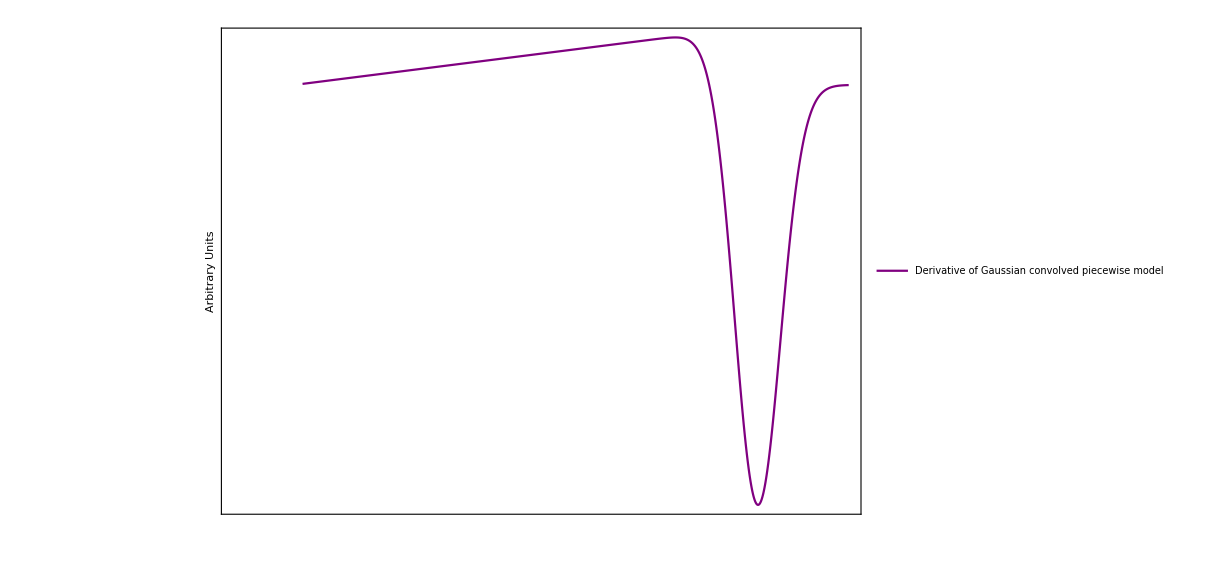

```mathematica
derfittedconvolvedmodelplot2 = Show[derfittedconvolvedmodelplot,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Purple},ImageSize->910,PlotLabel->Pane["",Alignment->Center],FrameLabel->{"  ","  "},Axes->False]
```

```mathematica
Overlay[{comboplot,derfittedconvolvedmodelplot2}]
```

-Graphics--Graphics-